```mathematica
(*This is a sheet with a rod extruding from the middle of it. 
I run two versions: rod has same diffusion coefficient as sheet, rod has different diffusion coefficient from sheet*)
epsilon = 0.05;sheet = MeshRegion[{{0,0},{0,1},{1,0},{1,1}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}];rod = MeshRegion[{{1,0.5-epsilon},{1,0.5+epsilon},{2,0.5-epsilon},{2,0.5+epsilon}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}];
reg = RegionUnion[sheet,rod];
```

```mathematica
(*Initial Temperature Distribution*)
kk = 50;
initFunc[x_,y_]:=kk*x^2*(x-2)^2*y^2*(y-1)^2;
```

```mathematica
(*Specify diffusion coefficients*)
alphaSheet  = 0.02; alphaRod=0.8;
diffFunc[x_]:=Piecewise[{{alphaSheet,x<1},{alphaRod,x>1}}];

(*Computes the system if entire region has same diffusion coefficient*)
valsUniformDiffusion = NDSolveValue[{D[u[t,x,y],t]==alphaSheet*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
valsNonUniformDiffusion = NDSolveValue[{D[u[t,x,y],t]==diffFunc[x]*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
```

```mathematica
(*Shows the results*)
Manipulate[Plot3D[{valsUniformDiffusion[t,x,y],
valsNonUniformDiffusion[t,x,y],
0,3},{x,y}∈reg,
PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]
```

```mathematica
yy=0.5;Manipulate[Plot[{valsUniformDiffusion[t,x,yy],valsNonUniformDiffusion[t,x,yy],0,3},{x,0,2},PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]
```

```mathematica
(*Derivatives with respect to x and y so we can see the fluxes*)
```

```mathematica
XderivUniformDiffusion[t_,x_,y_]:=D[valsUniformDiffusion[tV,xV,yV],xV]/.{tV->t,xV->x,yV->y};
XderivNonUniformDiffusion[t_,x_,y_]:=D[valsNonUniformDiffusion[tV,xV,yV],xV]/.{tV->t,xV->x,yV->y};
```

```mathematica
YderivUniformDiffusion[t_,x_,y_]:=D[valsUniformDiffusion[tV,xV,yV],yV]/.{tV->t,xV->x,yV->y};
YderivNonUniformDiffusion[t_,x_,y_]:=D[valsNonUniformDiffusion[tV,xV,yV],yV]/.{tV->t,xV->x,yV->y};
```

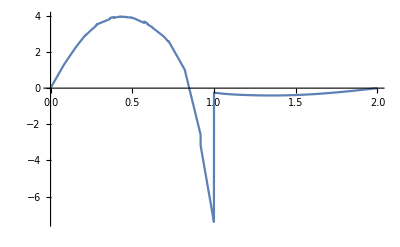

```mathematica
(*X Diffusion in middle of system, y=0.5, for nonuniform diffusion at t=0.4*)
tVV=0.4;
Plot[XderivNonUniformDiffusion[tVV,x,0.5],{x,0,2}]
```

```mathematica
(*X Diffusion in middle of system, y=0.5, for uniform diffusion as comparison at t=0.4*)
```

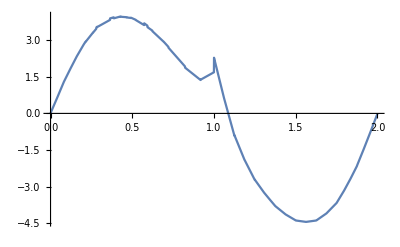

```mathematica
Plot[XderivUniformDiffusion[tVV,x,0.5],{x,0,2}]
```

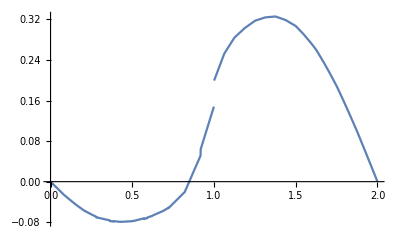

```mathematica
(*X Heat Flux in middle of system, y=0.5, for nonuniform diffusion at t=0.4*)
Plot[-XderivNonUniformDiffusion[tVV,x,0.5]*diffFunc[x],{x,0,2}]
```

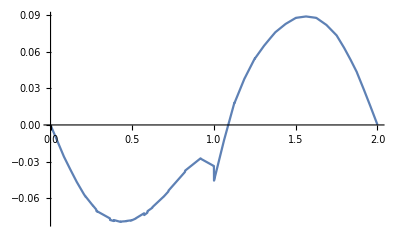

```mathematica
(*X Heat Flux in middle of system, y=0.5, for uniform diffusion as comparison at t=0.4*)
Plot[-XderivUniformDiffusion[tVV,x,0.5]*alphaSheet,{x,0,2}]
```

```mathematica
(*Diffusion at borders. should be near zero*)
Table[YderivNonUniformDiffusion[tVV,x,1],{x,0,1,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0],{x,0,1,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0.5-epsilon],{x,1,2,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0.5+epsilon],{x,1,2,.1}]
Table[XderivNonUniformDiffusion[tVV,0,y],{y,0,1,.1}]
Table[XderivNonUniformDiffusion[tVV,1,y],{y,0,0.5-epsilon,.1}]
Table[XderivNonUniformDiffusion[tVV,1,y],{y,0,0.5+epsilon,.1}]
Table[XderivNonUniformDiffusion[tVV,2,y],{y,0.5-epsilon,0.5+epsilon,.02}]
```

{-0.00728168,-0.016734,0.013887,-0.00451358,0.0270785,-0.00470745,0.0239446,-0.0635252,-0.0198483,-0.0345256,-0.146119}

{-0.0191278,0.0175708,0.0193435,0.0664701,-0.0329305,0.102237,0.0955793,0.0059862,0.0198704,0.00529009,0.0474396}

{-0.245519,0.0139008,-0.000424264,0.000334481,0.00114736,0.0000195524,-0.00107461,-0.000267976,0.00023582,0.000250442,0.000135665}

{0.246205,-0.0139961,0.000425562,-0.000334273,-0.00114735,-0.0000195514,0.00107461,0.000267976,-0.00023582,-0.000250442,-0.000135665}

{0.00386313,0.0172152,-0.0191949,-0.00543749,-0.00409226,0.0191656,-0.00171435,-0.0219027,-0.032798,0.0164088,-0.0230218}

{-0.0198019,-0.0687467,-0.0632015,-0.0990738,-2.13168}

{-0.0198019,-0.0687467,-0.0632015,-0.0990738,-2.13168,-7.42916}

{-0.000135346,-0.000135346,-0.000135346,-0.000135346,-0.000135346,-0.000135346}

```mathematica
(*Diffusion at borders for uniform system as comparison. should be near zero*)
```

```mathematica
Table[YderivUniformDiffusion[tVV,x,1],{x,0,1,.1}]
Table[YderivUniformDiffusion[tVV,x,0],{x,0,1,.1}]
Table[YderivUniformDiffusion[tVV,x,0.5-epsilon],{x,1,2,.1}]
Table[YderivUniformDiffusion[tVV,x,0.5+epsilon],{x,1,2,.1}]
Table[XderivUniformDiffusion[tVV,0,y],{y,0,1,.1}]
Table[XderivUniformDiffusion[tVV,1,y],{y,0,0.5-epsilon,.1}]
Table[XderivUniformDiffusion[tVV,1,y],{y,0,0.5+epsilon,.1}]
Table[XderivUniformDiffusion[tVV,2,y],{y,0.5-epsilon,0.5+epsilon,.02}]
```

{-0.00726872,-0.0167506,0.0138721,-0.00455659,0.0270642,-0.00481746,0.0238812,-0.0637146,-0.0198668,-0.0341691,-0.143961}

{-0.0191553,0.0175899,0.0193702,0.0665678,-0.0328357,0.102423,0.0958066,0.00611744,0.0198546,0.00505633,0.0471167}

{2.23048,-0.201891,-0.00812494,0.00712312,0.0170014,-0.00130037,-0.0219827,-0.00879332,0.00899434,0.0137245,0.00781551}

{-2.2308,0.201931,0.00812433,-0.00712325,-0.0170014,0.00130037,0.0219827,0.00879332,-0.00899434,-0.0137245,-0.00781551}

{0.00385588,0.0172257,-0.0191721,-0.00540536,-0.00405872,0.0191883,-0.00167582,-0.0218938,-0.0327836,0.0164196,-0.0230433}

{-0.0195113,-0.0672868,-0.0469894,-0.0199879,0.480447}

{-0.0195113,-0.0672868,-0.0469894,-0.0199879,0.480447,1.68438}

{-0.00801516,-0.00801516,-0.00801516,-0.00801516,-0.00801516,-0.00801516}

```mathematica
(*Total Energy of system at a few time points to make sure that is conserved*)
```

```mathematica
Table[NIntegrate[valsNonUniformDiffusion[curT,x,y],{x,y}∈reg],{curT,0.1,9.1,1}]
```

{1.05445,1.05445,1.05445,1.05445,1.05445,1.05445,1.05445,1.05445,1.05445,1.05445}

```mathematica
Table[NIntegrate[valsUniformDiffusion[curT,x,y],{x,y}∈reg],{curT,0.1,9.1,1}]
```

{1.05445,1.05445,1.05445,1.05445,1.05445,1.05445,1.05445,1.05445,1.05445,1.05445}